```mathematica
NFW[x_]:=Piecewise[{{1/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]), x≤ 1}, {1/(x^2-1)(1-2/(√(x^2-1))ArcTan[√((x-1)/(1+x))]), x>1}}]
MNFW[x_]:=Log[x/2]+Piecewise[{{2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))], x≤1}, {2/(√(x^2-1))ArcTan[√((x-1)/(1+x))], x>1}}]
```

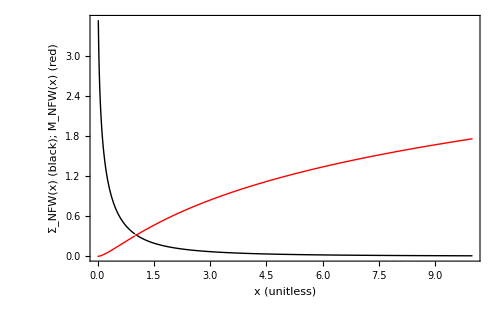

```mathematica
Plot[{NFW[x],MNFW[x]},{x,0,10},Frame->True,PlotStyle->{{Black,Thick},{Red, Thick}},FrameLabel->{"x (unitless)","Σ_NFW(x) (black); M_NFW(x) (red)","NFW Profile and Enclosed Mass at Normalized Scale" },LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18], ImageSize->500]
```

```mathematica
Integrate[NFW[R/r]R,{R,0,Rprime},Assumptions->Element[Rprime,Reals]&&Rprime>0]
```

```mathematica
Integrate[NFW[r x]x,{x,0,Rprime},Assumptions->Element[Rprime,Reals]&&Rprime>0]
```

```mathematica
Integrate[NFW[R]R,{R,0,x},Assumptions->Element[x,Reals]&&x>0]//FullSimplify
```

```mathematica
MNFW2[x_]:=Piecewise[{{2 √(1/(1-x^2)) ArcTanh[1/(√((1+x)/(1-x)))]+Log[x/2], x≤1}, {(2 ArcTan[√((-1+x)/(1+x))])/(√(-1+x^2))+Log[x/2], True}}]
```

```mathematica
MNFW3[x_]:=Log[x/2]+2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]
```

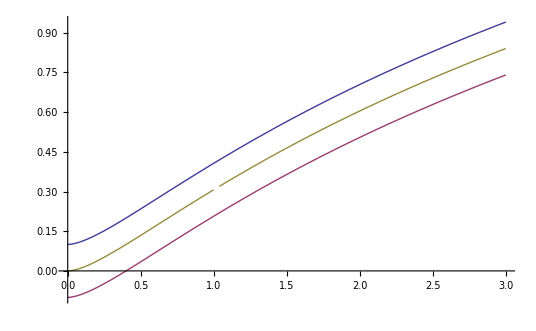

```mathematica
Plot[{2 √(1/(1-x^2)) ArcTanh[1/(√((1+x)/(1-x)))]+Log[x/2]+0.1,(2 ArcTan[√((-1+x)/(1+x))])/(√(-1+x^2))+Log[x/2]-0.1, MNFW2[x]},{x,0,3}]
```

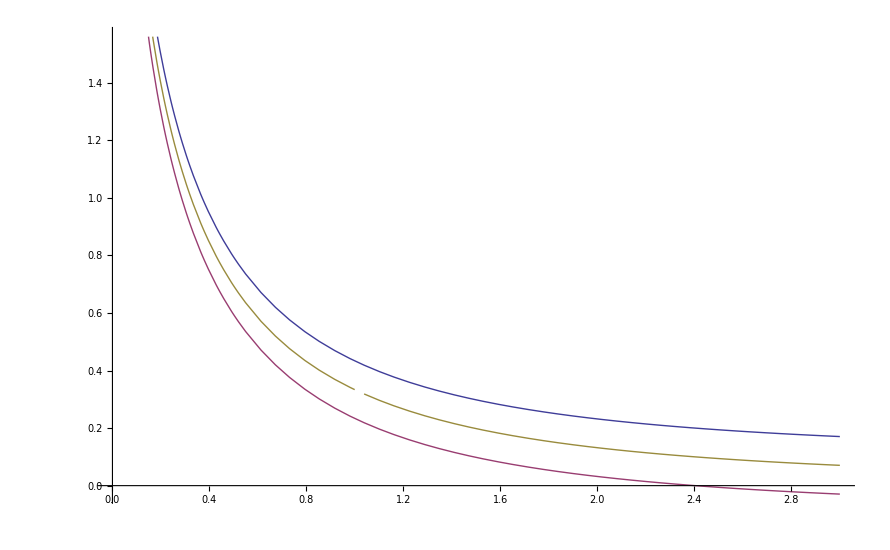

```mathematica
Plot[{1/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])+0.1,1/(x^2-1)(1-2/(√(x^2-1))ArcTan[√((x-1)/(1+x))])-0.1,NFW[x]},{x,0,3}]
```

```mathematica
f[x_]:=2/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])
```

```mathematica
MNFW3[x_]:=Log[x/2]+2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))]
PxPerRad=180/π 3600/0.03;
rs[M200_,c_]:=N[(4.302/67.8^2*10^3)^(1/3),10]*(M200)^(1/3)/c
N[(4.302/67.8^2*10^3)^(1/3),10];
rad[px_]:=(180/π 3600/0.03)^-1 px
ΩM=0.315;
ΩD=0.685;
ZEQ=3391;
H0=4424.778 ;
AngDiDist[z1_,z2_]:=H0/(z2+1)NIntegrate[1/(√(ΩM(1+z/ZEQ)z^3+ΩD)),{z,z1+1,z2+1}]

Dl=AngDiDist[0,0.3];
G=4.302;
deltac2[c_]:=1/(Log[1+c]-c/(1+c))
NFWPrefactor[M200_,c_]:=(PxPerRad*4*G*M200 *deltac2[c])/(9*Dl*10^5)
Alpha[px_,M200_,c_]:=NFWPrefactor[M200,c] MNFW3[rad[px] Dl/rs[M200,c]]/(rad[px]*px)
```

```mathematica
g[x_]:=4/x^2 Log[x/2]+Piecewise[{{8/(x^2 √(1-x^2)) ArcTanh[√((1-x)/(1+x))]-2/(x^2-1)+4/((x^2-1)√(1-x^2))ArcTanh[√((1-x)/(1+x))], x< 1}, {10/3, x==1}, {8/(x^2 √(x^2-1)) ArcTan[√((x-1)/(1+x))]-2/(x^2-1)+4/((x^2-1)^(3/2))ArcTan[√((x-1)/(1+x))], x>1}}] 

MBar[x_]:=4/x^2(Log[x/2]+Piecewise[{{2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))], x≤ 1}, {2/(√(x^2-1))ArcTan[√((x-1)/(1+x))], x>1}}])
```

```mathematica
MBar2[x_]:=4/x^2(Log[x/2]+2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])
MEnc[x_]:=2/(x^2-1)(1-2/(√(1-x^2))ArcTanh[√((1-x)/(1+x))])
```

```mathematica
h[x_]:=MBar2[x]-MEnc[x]
```

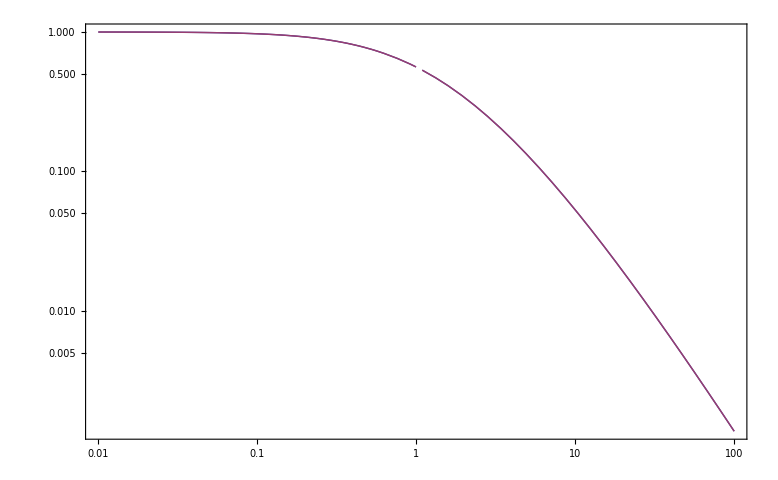

```mathematica
LogLogPlot[{g[x],h[x]},{x,0.01,100},Frame->True]
```

```mathematica
FindRoot[Alpha[x,20,2]==0.22,{x,150}]
```

{x→815.157}

```mathematica
file=SystemDialogInput["FileOpen"]
```

/home/dan/Desktop/jedisim3/log.txt

```mathematica
dat =Import["/home/dan/Desktop/jedisim3/log2.txt","TSV"];
```

```mathematica
dat⟦1⟧
```

{1,13001.,0.000859429,0.612634,0.173714}

```mathematica
dat2=dat⟦All,1;;2⟧;
```

```mathematica
dat2⟦1;;10⟧
```

{{1,13001.},{2,6500.49},{3,4333.66},{4,3250.24},{5,2600.19},{6,2166.83},{7,1857.28},{8,1625.12},{9,1444.55},{10,1300.1}}

```mathematica
Alpha2[px0_,px_,M200_,c_]:=NFWPrefactor[M200,c] MNFW3[rad[px0] Dl/rs[M200,c]]/(rad[px0]*px)
```

```mathematica
Alpha2[5909,0.5,20,2]
```

2600.04

```mathematica
deltac3[c_]:=c^3/(Log[1+c]-c/(1+c))
```

```mathematica
shearPrefactor[M200_,c_,H_,Dd_,Dds_,Ds_]:=100 H^2 rs[M200,c] deltac3[c]/((3*10^5)^2)(Dd*Dds)/Ds
```

```mathematica
sprefactor=shearPrefactor[20,4,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]
```

0.161411

```mathematica
shear[px_,M200_,c_]:=shearPrefactor[M200,c,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*g[rad[px] AngDiDist[0,0.3]/rs[M200,c]]
shear2[px_,M200_,c_]:=shearPrefactor[M200,c,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*h[rad[px] AngDiDist[0,0.3]/rs[M200,c]]
```

```mathematica
κ[px_,M200_,c_]:=shearPrefactor[M200,c,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*f[rad[px] AngDiDist[0,0.3]/rs[M200,c]]
```

```mathematica
shearX[x_,M200_,c_]:=shearPrefactor[M200,c,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*h[x]
κX[x_,M200_,c_]:=shearPrefactor[M200,c,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*f[x]
```

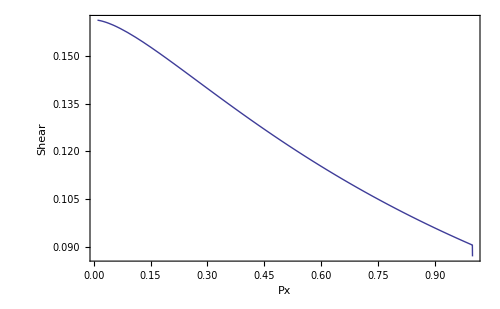

```mathematica
Plot[{shearPrefactor[20,4,67.80,AngDiDist[0,0.3],AngDiDist[0.3,1],AngDiDist[0,1]]*h[x]},{x,0.01,1},Frame->True,FrameLabel->{"Px","Shear"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18], ImageSize->500]
```

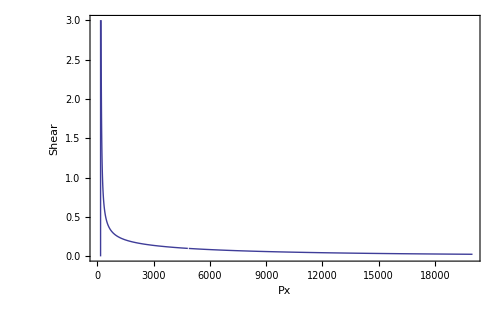

```mathematica
Plot[shear[px,20,4]/(1-κ[px,20,4]),{px,0.01,20000},Frame->True,FrameLabel->{"Px","Shear"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18],PlotRange->{0,3}, ImageSize->500]
```

```mathematica
x/.FindRoot[shear[x,10,4]/(1-κ[x,10,4])==#,{x,2000},MaxIterations->1000]&/@{0.19414713286400626,0.14736083651990353,0.08508508764016237,0.05775988789251338}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{679.226,1233.53,3396.75,5769.69}

```mathematica
{0,30,60,90,120,150}*π/180
```

```mathematica
{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6}//N
```

{0.,0.523599,1.0472,1.5708,2.0944,2.61799}

```mathematica
{0.2,0.15,0.1,0.05}
```

```mathematica
{0.2,0.15,0.1,0.05}
```

{0.184584,0.138438,0.0922919,0.0461459}

```mathematica
(1+RandomReal[{-1/10,1/10},4])
```

{1.04124,0.997474,0.909445,1.04304}

```mathematica
Thread[#1*#2&[(1+RandomReal[{-2/10,2/10},4]),{0.2,0.15,0.1,0.05}]]
```

{0.194147,0.147361,0.0850851,0.0577599}

```mathematica
4096*3/2
```

6144